```mathematica
Pattern[addition, {_,"+",_}]
```

addition:{_,+,_}

```mathematica
additionRules={__, "+",__}
```

{__,+,__}

```mathematica
MatchQ[{1, "+", 2}, additionRules]
```

True

```mathematica
commutativeGraph:={x,y} RelationGraph[MatchQ, {x, y}] (*Want to be able to define this functionally*)
```

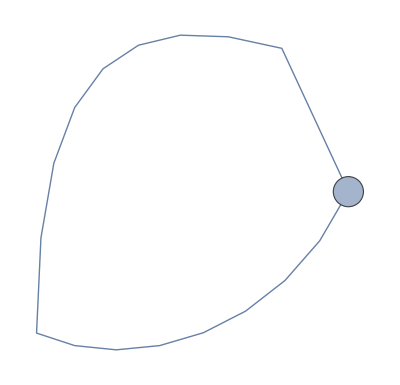

```mathematica
commutativeGraph[1+2, 2+1]
```

```mathematica
MatchQ[1+2,2+1]
```

True